This presentation uses Dynamics. Please enable them (Evaluation > Dynamic Updating Enabled), and evaluate the whole notebook (Evaluation > Evaluate Notebook).

(* Import the needed modules *)
AppendTo[$Path, NotebookDirectory[]];
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
Get["CubeSolver.wl"]
Get["CubeAnimate.wl"]
Get["CubeColors.wl"]
(* Create the cube used for demonstration purposes *)
cubeString = sampleStrings["start"];
cube3DPieces = GetPieces[cubeString];
cube3D = Dynamic[Generate3DCube[cube3DPieces]];

(* Display a fancy red button *)
Print[Button[Style[Text["Please click here to evaluate the notebook."],FontSize→24,FontColor→Red],NotebookEvaluate[EvaluationNotebook[],InsertResults->True],Method->"Queued"]]

Please click here to evaluate the notebook.

# DeathCube

## A Rubik’s Cube Solver implemented with the Mathematica language

Balugani Lorenzo - Benetton Alessandro - Cosenza Alessandra - Crespan Lorenzo -  Li Zhiguang - Mazzocato Luca

(* a cool image *)
Print[-Graphics-]

-Graphics-

## The Rubik’s Cube

The Rubik’s Cube is a classic puzzle game in which the player is tasked to un-scramble a scrambled cube, composed of 26 smaller cubes (cubelets) that have colored faces, in such a way that every face is made by cubelets of the same color. These cubelets will be referred, according to their classification, as:

Centers: centers only have a single visible face, and they are in a fixed position.

Edges: edges have two visible faces;

Corners: corners have three visible faces

The puzzle can be unscrambled in many ways, but it’s highly unadvised to do so without a proper algorithm. In order to solve a cube, the user must execute rotations on one of the cube’s faces or rotations on the whole cube, clockwise or counterclockwise (‘).

(* Set up the buttons for the playground *)
size = 24;
Print[Button[Text[Style["Left", FontSize→size]],cube3DPieces=RotateL[cube3DPieces];],Button[Text[Style["Left'", FontSize→size]],cube3DPieces=RotateLi[cube3DPieces];],Button[Text[Style["Right", FontSize→size]],cube3DPieces=RotateR[cube3DPieces];],Button[Text[Style["Right'", FontSize→size]],cube3DPieces=RotateRi[cube3DPieces];],Button[Text[Style["Up", FontSize→size]],cube3DPieces=RotateU[cube3DPieces];],Button[Text[Style["Up'", FontSize→size]],cube3DPieces=RotateUi[cube3DPieces];],Button[Text[Style["Down", FontSize→size]],cube3DPieces=RotateD[cube3DPieces];],Button[Text[Style["Down'", FontSize→size]],cube3DPieces=RotateDi[cube3DPieces];],Button[Text[Style["Front", FontSize→size]],cube3DPieces=RotateF[cube3DPieces];],Button[Text[Style["Front'", FontSize→size]],cube3DPieces=RotateFi[cube3DPieces];],Button[Text[Style["Back", FontSize→size]],cube3DPieces=RotateB[cube3DPieces];],Button[Text[Style["Back'", FontSize→size]],cube3DPieces=RotateBi[cube3DPieces];]];
Print[
Button[Text[Style["Rotate X", FontSize→size]],cube3DPieces=RotateX[cube3DPieces];],Button[Text[Style["Rotate X'", FontSize→size]],cube3DPieces=RotateXi[cube3DPieces];],Button[Text[Style["Rotate Y", FontSize→size]],cube3DPieces=RotateY[cube3DPieces];],Button[Text[Style["Rotate Y'", FontSize→size]],cube3DPieces=RotateYi[cube3DPieces];],Button[Text[Style["Rotate Z", FontSize→size]],cube3DPieces=RotateZ[cube3DPieces];],Button[Text[Style["Rotate Z'", FontSize→size]],cube3DPieces=RotateZi[cube3DPieces];],
Button[Text[Style["Reset", FontSize→size]],(cube3DPieces=GetPieces[sampleStrings["start"]];ResetSolutionMoves[];);]
]

LeftLeft'RightRight'UpUp'DownDown'FrontFront'BackBack'

Rotate XRotate X'Rotate YRotate Y'Rotate ZRotate Z'Reset

Visualize3DCube[cube3D];

-Graphics3D-

### Color blind checkpoint

If you suffer from the color blindness condition, a standard Rubik’s Cube may be completely unusable for you. You might need a special cube with different shapes on each face, or with colors that are right for your flavour of color blindness. Please select - accordingly - the cube color configuration that best suits you: if you are not affected, please move on.

Print[VisualizeColorSchemePicker[25]]
cube2D=Dynamic[Generate2DCube[sampleStrings["solved"]]];
Visualize2DCube[cube2D];

-Graphics-

## The beginner’s algorithm

The beginner’s algorithm is the easiest cube-solving algorithm, however not the fastest by far, and it’s the one that was chosen by the team to be implemented in this project.
The algorithm is composed of 7 steps, and each of them is taken care by a specific function in the CubeSolver module.

Reset[stage_]:=(
Switch[stage,
0, (cube3DPieces=GetPieces[sampleStrings["start"]];ResetSolutionMoves[];),
1, (cube3DPieces=GetPieces[sampleStrings["start"]]; WhiteCross[];ResetSolutionMoves[];),
2, (cube3DPieces=GetPieces[sampleStrings["start"]]; WhiteCross[];PlaceWhiteCorner[];ResetSolutionMoves[];),
3, (cube3DPieces=GetPieces[sampleStrings["start"]]; WhiteCross[];PlaceWhiteCorner[];SecondLayer[];ResetSolutionMoves[];),
4, (cube3DPieces=GetPieces[sampleStrings["start"]]; WhiteCross[];PlaceWhiteCorner[];SecondLayer[];YellowCross[];ResetSolutionMoves[];),
5, (cube3DPieces=GetPieces[sampleStrings["start"]]; WhiteCross[];PlaceWhiteCorner[];SecondLayer[];YellowCross[];YellowEdges[];ResetSolutionMoves[];),
6,(cube3DPieces=GetPieces[sampleStrings["start"]]; WhiteCross[];PlaceWhiteCorner[];SecondLayer[];YellowCross[];YellowEdges[];YellowCorners[];ResetSolutionMoves[];)
]
)
DisplayHelp[]:=(Print[MessageDialog[Style[Text["U: Rotation of the upper layer;
D: Rotation of the bottom layer;
F: Rotation of the front layer;
B: Rotation of the back layer;
L: Rotation of the left layer;
R: Rotation of the Right layer;
X:Rotaion of the cube on the X axis;
Y: Rotation of the cube on the Y axis;
Z: Rotation of the cube on the Z axis;

       Moves that end with 'i', such as 'Bi' mean that the rotation must be counterclockwise."], FontSize→18]]]

)

### Step 1 - White Cross

This step focuses on creating a white cross on the white face of the cube. It begins on the yellow face, in which a “daisy” is formed (yellow center surrounded by white faces), and then, for each of those white faces, the top layer gets rotated until its other face is on the right face. Then, rotate in such a way that the white face is on the bottom of the cube.
Once this process has been completed for all faces, the step is complete, and the upwards face becomes the white one.

This step is taken care by the WhiteCross function in the solver package.

(* This section is the same in the other slides with slight variations, so it will only be discussed here. It displays buttons that allow to see the steps of the algorithm and to go back. *)
Print[Button[Text[Style["Show step", FontSize→size]],(Reset[0];WhiteCross[];);],
Button[Text[Style["Reset", FontSize→size]],Reset[0];],
Button[Text[Style["?", FontSize→size]],DisplayHelp[];]
]
Visualize3DCube[cube3D];
Print[Dynamic[GetSolutionMoves[]]]

Show stepReset?

-Graphics3D-

8ss5e_shm46FrontEndObject[LinkObject["8ss5e_shm", 111, 6]]4646

### Step 2 - White corners

The most optimal way to solve this step depends on the particular situation the cube is in. However, since learnability is far more important than optimality in our case, we went with the safe and always working R’D’RD move. 
Before all of this, however, the white corner must be taken to the bottom layer, and once that’s in place the moves can begin. Eventually, the white corner will be in place, and the focus can shift to the next one.

This step is taken care by the PlaceWhiteCorner function in the solver package.

Print[Button[Text[Style["Show step", FontSize→size]],(Reset[1];PlaceWhiteCorner[];);],
Button[Text[Style["Reset", FontSize→size]],(Reset[1]);],
Button[Text[Style["?", FontSize→size]],DisplayHelp[];]
]
Visualize3DCube[cube3D];
Print[Dynamic[GetSolutionMoves[]]]

Show stepReset?

-Graphics3D-

### Step 3 - Second layer

The second layer requires two different procedures, called the “Right” and “Left” algorithm. These two differ in the set of moves, and perhaps the hardest part is choosing the right one.
First of all, rotate the cube so that the yellow center is the one on the upwards face, and then, for each of the edges on the yellow face, check where the upper face of the edge should go: if the face is on the left, choose the “Left” algorithm, and so on. 
If everything fails, attempt a void move by executing the “Right” one.

Right algorithm: U R U’ R’ U’ F’ U F

Left algorithm: U’ L’ U L U F U’ F’

This step is taken care by the SecondLayer function in the solver package .

Print[Button[Text[Style["Show step", FontSize→size]],(Reset[2];SecondLayer[];);],
Button[Text[Style["Reset", FontSize→size]],(Reset[2]);],
Button[Text[Style["?", FontSize→size]],DisplayHelp[];]
]
Visualize3DCube[cube3D];
Print[Dynamic[GetSolutionMoves[]]]

Show stepReset?

-Graphics3D-

### Step 4 - Yellow cross

With the bottom layers dealt with, the top layer (yellow facing upwards) stands alone. The first step is creating the yellow cross, and this requires going through 4 different configurations:

The “Dot”, meaning only the center is yellow on the yellow face;

The “Reverse L”, meaning a reverse L shape has formed on the yellow face;

The “I”, meaning an horizontal line has formed on the yellow face;

The “Cross”;

These configurations are sequential, and not all may appear (for example, chance may have formed an L, skipping the need for the first part).
 All that needs to be done is to execute the F R U R’ U’ F’ steps, rotating the cube in such a way you’re facing the edge that you’re trying to place.
 
This step is taken care by the YellowCross function in the solver package.

Print[Button[Text[Style["Show step", FontSize→size]],(Reset[3];YellowCross[];);],
Button[Text[Style["Reset", FontSize→size]],(Reset[3]);],
Button[Text[Style["?", FontSize→size]],DisplayHelp[];]
]
Visualize3DCube[cube3D];
Print[Dynamic[GetSolutionMoves[]]]

Show stepReset?

-Graphics3D-

### Step 5 - Swap the yellow edges

The edges may now be in place, but they’re not on the right face (or at least, not entirely): their other face must be placed accordingly. 
First, rotate the top layer, choosing which cubelet’s face will be placed on the correct face, and then perform R U R’ U R U U R’ U. This move may be required to be done twice, rotating the cube on the horizontal axis two times.

This step is taken care by the YellowEdges function in the solver package.

Print[Button[Text[Style["Show step", FontSize→size]],(Reset[4];YellowEdges[];);],
Button[Text[Style["Right", FontSize→size]],(Reset[4]);],
Button[Text[Style["?", FontSize→size]],DisplayHelp[];]
]
Visualize3DCube[cube3D];
Print[Dynamic[GetSolutionMoves[]]]

Show stepRight?

-Graphics3D-

### Step 6 - Position yellow corners

In this step we start placing the corners on the yellow face. Doing so requires facing a yellow corner who’s already in place and performing the moves U R U’ L’ U R’ U’ L until all the corners are correctly placed.
If no corners are available to be used as a starting position, iterate the same moves until one appears.

This step is taken care by the YellowCorners function in the solver package.

Print[Button[Text[Style["Show step", FontSize→size]],(Reset[5];YellowCorners[];);],
Button[Text[Style["Reset", FontSize→size]],(Reset[5]);],
Button[Text[Style["?", FontSize→size]],DisplayHelp[];]
]
Visualize3DCube[cube3D];
Print[Dynamic[GetSolutionMoves[]]]

Show stepReset?

-Graphics3D-

### Step 7 - Final move

To complete the algorithm, perform R’ D’ R D until the yellow face is complete. Eventually, the cube will be solved.
Sometimes a twist of the upper layer is required to correctly place all the cubelets.

This step is taken care by the YellowCornersOrientation function in the solver package.

Print[Button[Text[Style["Show step", FontSize→size]],(Reset[6];YellowCornersOrientation[];);],
Button[Text[Style["Reset", FontSize→size]],(Reset[6]);],
Button[Text[Style["?", FontSize→size]],DisplayHelp[];]
]

Visualize3DCube[cube3D];
Print[Dynamic[GetSolutionMoves[]]]

Show stepReset?

-Graphics3D-

## About this project

This project was developed as part of the course in Computational Mathematics at the University of Bologna, AY 2021 - 2022, and its aim is to show and teach users how to navigate and solve the Rubik’s Cube. 
Entirely written in Mathematica, the project spans over 6 different modules, and the load of the work was split among the six different members of the team: while sizeable, since the task at hand was quite the undertaking, everyone was fully involved in all of the development phases.
In order to keep everyone updated on the state of the project, tools such as Atlassian Jira and Git were used (and were more times than one lifesavers).

### “This is going to be easy, right?” “...No.”

Since everyone was fully invested in the idea, developing the project has been challenging but fun: this, however, does not mean it was not complicated. The more we worked on it, the more functionalities we wanted to add: what in the beginning just was a simple solver with a barebone representation and cube input, after a week was nowhere near what it was at first. To fullfill our satisfaction, it was clear that in the final product a 3D representation was needed, with animations and a easy to use input system.
To fully understand the complexity, the following slides will focus on a module at a time.

### CubeAcquire

CubeAcquire is the module that handles interactions with the user in terms of cube configuration input. This can be done in both a graphical and textual approach: while the first is more comfortable and immediate, the latter makes the application accessible.
The input is checked to preemptively locate invalid input cubes by confronting the input cubelets with the ones from a solved and correct cube.

### CubeAnimate

CubeAnimate is the module that handles cube animations.
In order to animate the cube, a list of moves must be set, and then they can be accessed using the RubikNext and RubikPrev functions.
The animation is done by the AnimateMove function, which requires as parameters the move to be animated and the number of animation frames, and the rotations of the layers is accomplished with rotation matrices.

### CubeColors

CubeColors is the module that handles the conversions between colors, letters and images.
Since we wanted to have our application to be used also by colorblind people, there’s the option to have on the faces, instead of colours, textures.
Internally all the modules use a representation-agnostic approach, using letters that the renderer then maps to the correct colour or texture.

### CubeCore

CubeCore is the heart of the whole package, and does a whole lot of different things:

Defines the data structure used to describe the cube;

Keeps track of the moves that have been done on the cube;

From a string it generates the cubelets;

Implements the cube manipulation functions, on a layer or on the whole cube;

Optimizations;

### CubeSolver

CubeSolver is the module that implements the Beginner’s Algorithm in all of its steps. The solution is then optimized by the Core, which means that - for example - 3 consecutive L moves will be replaced by a single L’.

### CubeVisualize

CubeVisualize is the module that handles the graphical representation of the cube, both in a 2D (Visualize2DCube) and 3D (Visualize3DCube) manner. For compatibility reasons, the rendering engine has been set to use the Mesa renderer, and to the best of our knowledge is not possible to use hardware acceleration.
The “exploded” (or “flattened”) 2D view is mainly used for input purposes using the color picker.
In the 3D view, all the cubes are polygonal meshes that are created when the cube is instantiated.

### Dependency Graph

(* Dependency graph *)
Print[-Graphics-]

-Graphics-

## Trying out the application

This presentation serves as a way to allow users to interact with our application. In the following slides, you will be prompted to enter the cube configuration, and then you’ll see the solution step by step with an animation. Firstly, however, please click the button below in order to reset the cube for the cube editor.

Print[Button[Style[Text["Reset cube"], FontSize→size], (
cube3DPieces=GetPieces[sampleStrings["start"]]; ResetSolutionMoves[];
)]]

Reset cube

### Cube input

VisualizeColorPickerBox[];

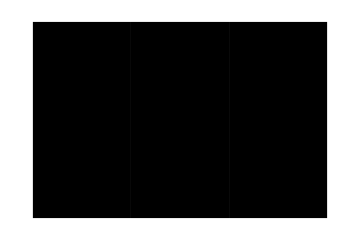
Color Picker
-Graphics-Current Color
-Graphics-

Print[VisualizeInput2DCube[]]

-Graphics-

Enter the cube configuration by choosing a color and then clicking on the face you want to paint. To check and save the cube, click on “Validate cube”. For accessibility purposes, a direct cube string input can be inserted: to save that kind of input, click the “check” button instead.

Print[Button[Style[Text["Validate cube"] ,FontSize->size],(If[ValidateCubeInput[]== True, (MessageDialog["Cube configuration is valid. Cube has been saved."];cube3DPieces=GetPieces[Cube2DToString[]]),MessageDialog["Cube configuration is not valid."]])],
Button[Style[Text["Load default"] ,FontSize->size],cube3DPieces=GetPieces[sampleStrings["start"]]]
]

Validate cubeLoad default

InputHelp[]:=(MessageDialog[Style[Text["W: White;
O: Orange;
G: Green
R:Red;
B: Blue;
Y: Yellow;

                       0  1  2
                       3  4  5
                       6  7  8
      9 10 11 12 13 14 15 16 17 18 19 20
     21 22 23 24 25 26 27 28 29 30 31 32
     33 34 35 36 37 38 39 40 41 42 43 44
                      45 46 47
                      48 49 50
                      51 52 53
	"], FontSize→16]]);
checkLength[x_]:=(If[Length[Characters[x]]==54,(MessageDialog["String "<>x<>" is a valid input."]; Return[True]),If[Length[Characters[x]]>54,MessageDialog["String "<>x<>" is not an acceptable input (too long, 54 characters reqired)"],MessageDialog["String "<>x<>" is not an acceptable input (too short, 54 characters required)"]]];Return[False];)
stringaInput="WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY";
Print[Grid[{{InputField[Dynamic[stringaInput],String],Button[Style[Text["Check"],FontSize→size],(If[checkLength[stringaInput]==True,cube3DPieces=GetPieces[stringaInput]]),ImageSize->100],Button[Style[Text["?"], FontSize→size],InputHelp[],ImageSize->100]}}]]

| Check | ?

### Cube solver

Visualize3DCube[Dynamic[cube3D]];
Print[Button[Style[Text["Show moves"], FontSize→size],MessageDialog[Dynamic[OptimizeMoveString[GetSolutionMoves[]]]]]]

-Graphics3D-

Show moves

Print[Button[Style[Text["Solve"],FontSize->size],(
bak = cube3DPieces;
ResetSolutionMoves[];
SolveCube[];
SetResolutionMoves[OptimizeMoveString[GetSolutionMoves[]]];
cube3DPieces = bak;)]
]

Solve

Print[
Button[Style[Text["Prev"],FontSize->size],
DelOut[];
RubikPrev[fps];
,Enabled→Dynamic[HasPrevMove[]]],
Button[Style[Text["Next"],FontSize→size], 
DelOut[];
RubikNext[fps];
,Enabled→Dynamic[HasNextMove[]]],
"Animation Rate: ", 
fps = 1.5;
Slider[Dynamic[fps], {0.1, 2, 0.1}],
Dynamic[fps]
]

PrevNextAnimation Rate:

## Difficulties & Challenges

The DeathCube project has been a fun but challenging exercise for the whole team - and most importantly the first big project that any of us has developed in Mathematica. The challenges were many, from understanding how to implement the Beginner’s Algorithm in such a way it would use Mathematica’s feature set at its fullest to learning how to build, display and animate 3D meshes. All the challenges were completed within deadline, and we are really pleased with how everything turned out.

However, the team encountered unexpected difficulties:

The Mathematica IDE: the IDE is maybe a bit too limited (if compared with tools such as IDEA from Intellij), and the debugging tools are not as powerful as someone would desire. The stacktrace information is not really helpful either, since it does not display where the issue is;

Dynamics weird behaviour: dynamics get evaluated only if they are “seen”, and seem to act weirdly if in the context of a presentation notebook;

## Sitography

During the development, these sources were consulted by the team:

The Mathematica documentation;

The Rubik's Cube Puzzle Wiki;

Rubiks.com;

Pglass Python Cube Solver, as a guideline for data structures;

# Thanks for your attention.

The DeathCube teams hopes you’ve found our work useful, or at least interesting. The source code is available on github.